# Mathematica 演習(2)

## 直線のパラメーター表示 （ベクトルの表記と演算の復習）

```mathematica
{2,1}+t*{1,-3}
```

{2+t,1-3 t}

## Plot コマンド

### y=f(x) のグラフ

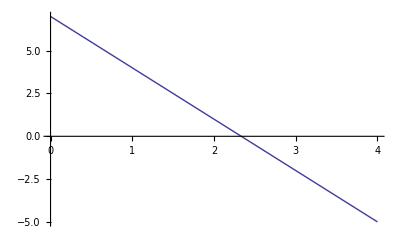

```mathematica
Plot[-3*x+7,{x,0,4}]
```

### パラメーター表示された図形の描画

```mathematica
ParametricPlot[{2,1}+t*{1,-3},{t,-2,2}]
```

-Graphics-

## 行列の演算

### 行列の表記

```mathematica
A={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
A
```

{{1,2},{3,4}}

```mathematica
A//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
B={{-1,2},{3,1}}
```

{{-1,2},{3,1}}

```mathematica
B//MatrixForm
```

(-1 | 2
3 | 1)

### 和と差，実数倍

```mathematica
A+B//MatrixForm
```

(0 | 4
6 | 5)

```mathematica
A-B//MatrixForm
```

(2 | 0
0 | 3)

```mathematica
3*B//MatrixForm
```

(-3 | 6
9 | 3)

### 積

```mathematica
A.B//MatrixForm
```

(5 | 4
9 | 10)

### 逆行列

```mathematica
Inverse[A]//MatrixForm
```

(-2 | 1
3/2 | -1/2)

```mathematica
A.Inverse[A]//MatrixForm
```

(1 | 0
0 | 1)

### 行列の転置

```mathematica
Transpose[A]//MatrixForm
```

(1 | 3
2 | 4)

### 行列式

```mathematica
Det[A]
```

-2

```mathematica
Det[B]
```

-7

### 直線を線形変換する

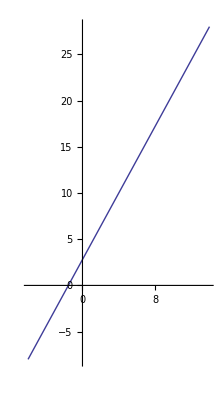

```mathematica
ParametricPlot[A.{2+t,1-3 t},{t,-2,2}]
```

```mathematica
c={{3,1},{-6,-2}}
```

{{3,1},{-6,-2}}

```mathematica
c//MatrixForm
```

(3 | 1
-6 | -2)

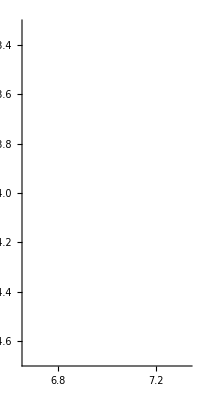

```mathematica
ParametricPlot[c.{2+t,1-3 t},{t,-2,2}]
```

### 回転行列による線形変換

```mathematica
R[s_]={{Cos[s],-Sin[s]},{Sin[s],Cos[s]}}
```

{{Cos[s],-Sin[s]},{Sin[s],Cos[s]}}

```mathematica
R[s]
```

{{Cos[s],-Sin[s]},{Sin[s],Cos[s]}}

```mathematica
R[Pi/3]//MatrixForm
```

(1/2 | -(√3)/2
(√3)/2 | 1/2)

```mathematica
Manipulate[ParametricPlot[R[s].{2+t,1-3 t},{t,-2,2},PlotRange->{{-5,5},{-5,5}}],{s,0,2*Pi},SaveDefinitions->True]
```